```mathematica
SetDirectory["C:\\Users\\benja\\OneDrive\\Documents\\GitHub\\KhovanovLaplacian\\basic_khovanov_testing"]
<< KnotTheory`
<< KhovanovLaplacian`
```

C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing

Get::path: ParentDirectory[File] in $Path is not a string.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ParentDirectory[File],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ParentDirectory[File],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory], should be a valid string or File.

General::stop: Further output of FileInformation::badfile will be suppressed during this calculation.

ReplaceAll::reps: {AbsoluteFileName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\OneDrive\DOCUME~1\GitHub\KHOVAN~1\BASIC_~1\KNOTTH~1,Archive→True,BlockCount→Missing[NotAvailable],BlockSize→Missing[NotAvailable],ByteCount→12288,Compressed→Missing[NotAvailable],CreationDate→DateObject[{2024,3,13,15,49,29.},Instant,Gregorian,-5.],DirectoryName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing,Encrypted→Missing[NotAvailable],«23»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParentDirectory::nums: Argument File/.{AbsoluteFileName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\OneDrive\DOCUME~1\GitHub\KHOVAN~1\BASIC_~1\KNOTTH~1,Archive→True,BlockCount→Missing[NotAvailable],BlockSize→Missing[NotAvailable],ByteCount→12288,Compressed→Missing[NotAvailable],CreationDate→DateObject[{2024,3,13,15,49,29.},Instant,Gregorian,-5.],DirectoryName→C:\Users\benja\OneDrive\Documents\GitHub\KhovanovLaplacian\basic_khovanov_testing,Encrypted→Missing[NotAvailable],«23»} should be a positive machine-size integer, a nonempty string, or a File specification.

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Get::path: ParentDirectory[File] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol CreateWikiConnection in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol WikiGetPageText in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

DeclarePackage::aldec: Symbol WikiGetPageTexts in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,WikiUploadFile,WikiUserName,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

General::stop: Further output of DeclarePackage::aldec will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[WikiGetPageText[Invariant_Definition_Table],<tr>].

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads StringSplit and List at positions 1 and 2 are expected to be the same.

Loading KhovanovLaplacian`...

PD[X[1,5,2,4],X[5,3,6,2],X[3,1,4,6]]

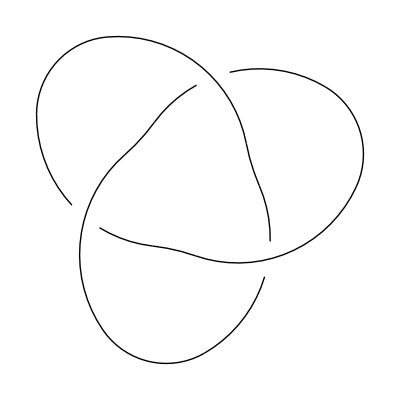

{{{0.},{6.,0.},{3.}},{{6.,3.,3.},{6.,6.,3.}},{{3.,3.,3.},{6.,6.,5.,2.,2.,-2.38512×10^-16},{4.,1.,1.}},{{3.},{5.,2.,2.},{4.,1.,1.},{0.}}}

```mathematica
trefoil = PD[X[1,5,2,4],X[5,3,6,2],X[3,1,4,6]] (*x-z projection leading to right handed trefoil with standard diagram*)
Show[DrawPD[trefoil]]
s1 = qSpectraAllEigs[trefoil]
```

## Form an Interesting Dirac operator, quantum grading 3.

```mathematica
CC[trefoil,-1,3]
CC[trefoil,0,3]
CC[trefoil,1,3]
CC[trefoil,2,3]
CC[trefoil,3,3]
CC[trefoil,4,3]
```

{0}

{v[0,0,0] vm[2] vp[1],v[0,0,0] vm[1] vp[2]}

{v[0,0,1] vm[1],v[0,1,0] vm[1],v[1,0,0] vm[1]}

{v[0,1,1] vm[1] vm[3],v[1,0,1] vm[1] vm[2],v[1,1,0] vm[1] vm[2]}

{v[1,1,1] vm[1] vm[2] vm[3]}

{0}

```mathematica
GetDQ[trefoil,-1,3]// MatrixForm
GetDQ[trefoil,0,3]// MatrixForm
GetDQ[trefoil,1,3]// MatrixForm
GetDQ[trefoil,2,3]// MatrixForm
GetDQ[trefoil,3,3]// MatrixForm
GetDQ[trefoil,4,3] // MatrixForm
```

(0)

(0
0)

(1 | 1
1 | 1
1 | 1)

(1 | -1 | 0
1 | 0 | -1
0 | 1 | -1)

(1 | -1 | 1)

(0)

```mathematica
dirac1 = qDirac[trefoil,4,3]
dirac1 // MatrixForm
Eigenvalues[qDirac[trefoil,4,3]]
```

{{0,0,1,1,1,0,0,0,0},{0,0,1,1,1,0,0,0,0},{1,1,0,0,0,1,1,0,0},{1,1,0,0,0,-1,0,1,0},{1,1,0,0,0,0,-1,-1,0},{0,0,1,-1,0,0,0,0,1},{0,0,1,0,-1,0,0,0,-1},{0,0,0,1,-1,0,0,0,1},{0,0,0,0,0,1,-1,1,0}}

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0)

{-√6,√6,-√3,-√3,-√3,√3,√3,√3,0}

Get::path: ParentDirectory[File] in $Path is not a string.

KnotTheory::loading: Loading precomputed data in PD4Knots`.

PD[X[4,2,5,1],X[6,4,1,3],X[2,6,3,5]]

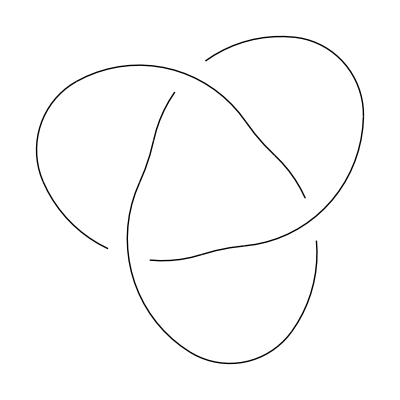

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0)

```mathematica
trefoil2 = Mirror[PD[Knot[3,1]]]
Show[DrawPD[trefoil2]]
dirac2 = qDirac[trefoil2,4,3];
dirac2 //MatrixForm
```

```mathematica
Eigenvalues[dirac1]
Eigenvalues[dirac2]
```

{-√6,√6,-√3,-√3,-√3,√3,√3,√3,0}

{-√6,√6,-√3,-√3,-√3,√3,√3,√3,0}

```mathematica
qDiracPrint[trefoil]
```

qDirac[0,1] =

(0)

qDirac[0,3] =

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

qDirac[0,5] =

(0 | 1 | 1 | 1
1 | 0 | 0 | 0
1 | 0 | 0 | 0
1 | 0 | 0 | 0)

qDirac[1,3] =

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0)

qDirac[1,5] =

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0)

qDirac[2,3] =

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0)

qDirac[2,5] =

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0)

qDirac[2,7] =

(0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | -1 | 1 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0)

qDirac[3,3] =

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0)

qDirac[3,5] =

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0)

qDirac[3,7] =

(0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | -1 | 1 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0)

qDirac[3,9] =

(0)

{{{{0}},{{0,0,1,1,1},{0,0,1,1,1},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0}},{{0,1,1,1},{1,0,0,0},{1,0,0,0},{1,0,0,0}}},{{{0,0,1,1,1,0,0,0},{0,0,1,1,1,0,0,0},{1,1,0,0,0,1,1,0},{1,1,0,0,0,-1,0,1},{1,1,0,0,0,0,-1,-1},{0,0,1,-1,0,0,0,0},{0,0,1,0,-1,0,0,0},{0,0,0,1,-1,0,0,0}},{{0,1,1,1,0,0,0,0,0,0},{1,0,0,0,1,1,1,1,0,0},{1,0,0,0,-1,-1,0,0,1,1},{1,0,0,0,0,0,-1,-1,-1,-1},{0,1,-1,0,0,0,0,0,0,0},{0,1,-1,0,0,0,0,0,0,0},{0,1,0,-1,0,0,0,0,0,0},{0,1,0,-1,0,0,0,0,0,0},{0,0,1,-1,0,0,0,0,0,0},{0,0,1,-1,0,0,0,0,0,0}}},{{{0,0,1,1,1,0,0,0,0},{0,0,1,1,1,0,0,0,0},{1,1,0,0,0,1,1,0,0},{1,1,0,0,0,-1,0,1,0},{1,1,0,0,0,0,-1,-1,0},{0,0,1,-1,0,0,0,0,1},{0,0,1,0,-1,0,0,0,-1},{0,0,0,1,-1,0,0,0,1},{0,0,0,0,0,1,-1,1,0}},{{0,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,1,1,0,0,0,0,0},{1,0,0,0,-1,-1,0,0,1,1,0,0,0},{1,0,0,0,0,0,-1,-1,-1,-1,0,0,0},{0,1,-1,0,0,0,0,0,0,0,1,1,0},{0,1,-1,0,0,0,0,0,0,0,0,0,1},{0,1,0,-1,0,0,0,0,0,0,-1,0,0},{0,1,0,-1,0,0,0,0,0,0,0,-1,-1},{0,0,1,-1,0,0,0,0,0,0,1,0,1},{0,0,1,-1,0,0,0,0,0,0,0,1,0},{0,0,0,0,1,0,-1,0,1,0,0,0,0},{0,0,0,0,1,0,0,-1,0,1,0,0,0},{0,0,0,0,0,1,0,-1,1,0,0,0,0}},{{0,0,0,0,1,1},{0,0,0,-1,-1,0},{0,0,0,1,0,1},{0,-1,1,0,0,0},{1,-1,0,0,0,0},{1,0,1,0,0,0}}},{{{0,0,1,1,1,0,0,0,0},{0,0,1,1,1,0,0,0,0},{1,1,0,0,0,1,1,0,0},{1,1,0,0,0,-1,0,1,0},{1,1,0,0,0,0,-1,-1,0},{0,0,1,-1,0,0,0,0,1},{0,0,1,0,-1,0,0,0,-1},{0,0,0,1,-1,0,0,0,1},{0,0,0,0,0,1,-1,1,0}},{{0,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,1,1,0,0,0,0,0},{1,0,0,0,-1,-1,0,0,1,1,0,0,0},{1,0,0,0,0,0,-1,-1,-1,-1,0,0,0},{0,1,-1,0,0,0,0,0,0,0,1,1,0},{0,1,-1,0,0,0,0,0,0,0,0,0,1},{0,1,0,-1,0,0,0,0,0,0,-1,0,0},{0,1,0,-1,0,0,0,0,0,0,0,-1,-1},{0,0,1,-1,0,0,0,0,0,0,1,0,1},{0,0,1,-1,0,0,0,0,0,0,0,1,0},{0,0,0,0,1,0,-1,0,1,0,0,0,0},{0,0,0,0,1,0,0,-1,0,1,0,0,0},{0,0,0,0,0,1,0,-1,1,0,0,0,0}},{{0,0,0,0,1,1},{0,0,0,-1,-1,0},{0,0,0,1,0,1},{0,-1,1,0,0,0},{1,-1,0,0,0,0},{1,0,1,0,0,0}},{{0}}}}

```mathematica
qDirac[trefoil,3,1] // MatrixForm
qDirac[trefoil,3,3] // MatrixForm
qDirac[trefoil,3,5] // MatrixForm
qDirac[trefoil,3,7] // MatrixForm
```

(0)

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0)

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 0 | 1 | 0 | 1
0 | -1 | 1 | 0 | 0 | 0
1 | -1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0)

```mathematica
diracsquare1 = MatrixPower[qDirac[trefoil,3,1],2] ;
diracsquare3 = MatrixPower[qDirac[trefoil,3,3],2] ;
diracsquare5 = MatrixPower[qDirac[trefoil,3,5],2] ;
diracsquare7 = MatrixPower[qDirac[trefoil,3,7],2] ;
diracsquare1 // MatrixForm
diracsquare3 // MatrixForm
diracsquare5 // MatrixForm
diracsquare7 // MatrixForm
Eigenvalues[diracsquare1]
Eigenvalues[diracsquare3]
Eigenvalues[diracsquare5]
Eigenvalues[diracsquare7]
```

(0)

(3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 4 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | -1 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 3 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 3 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 2 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 3)

(2 | -1 | 1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0
1 | -1 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 1 | 1
0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 1 | 1 | 2)

{0}

{6,6,3,3,3,3,3,3,0}

{6,6,6,6,5,5,3,3,2,2,2,2,0}

{4,4,1,1,1,1}

```mathematica
qSpectraAllEigs[trefoil]
```

{{{0.},{6.,0.},{3.}},{{6.,3.,3.},{6.,6.,3.}},{{3.,3.,3.},{6.,6.,5.,2.,2.,-2.38512×10^-16},{4.,1.,1.}},{{3.},{5.,2.,2.},{4.,1.,1.},{0.}}}

## Compare Dirac squares with Laplacians side by side

```mathematica
qDirac[trefoil,0,1] // MatrixForm
qLapNew[trefoil,0,1]//MatrixForm
```

(0)

(0)

```mathematica
qDirac[trefoil,0,3] // MatrixForm
Eigenvalues[qDirac[trefoil,0,3] ]
Eigensystem[qDirac[trefoil,0,3] ]

qDirac[trefoil,1,3] // MatrixForm
Eigenvalues[qDirac[trefoil,1,3] ]
Eigensystem[qDirac[trefoil,1,3] ]

MatrixPower[qDirac[trefoil,0,3],2] //MatrixForm
Eigenvalues[MatrixPower[qDirac[trefoil,0,3],2]]


MatrixPower[qDirac[trefoil,1,3],2] //MatrixForm
Eigenvalues[MatrixPower[qDirac[trefoil,1,3],2]]

qLapNew[trefoil,0,3]//MatrixForm
Eigenvalues[qLapNew[trefoil,0,3]]

qLapNew[trefoil,1,3]//MatrixForm
Eigenvalues[qLapNew[trefoil,1,3]]

Lup23 = Transpose[GetDQ[trefoil,2,3]].GetDQ[trefoil,2,3]; (*Expect that \Delta_{trefoil,up}^{2,3} is in (D_{trefoil}^{1,3})^2 *)
Lup23 // MatrixForm
Eigenvalues[Lup23]

qLapNew[trefoil,2,3]//MatrixForm  (*Do not expect \Delta_{trefoil}^{2,3}*)
qLapNew[trefoil,3,3]//MatrixForm
```

(0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0)

{-√6,√6,0,0,0}

{{-√6,√6,0,0,0},{{-√(3/2),-√(3/2),1,1,1},{√(3/2),√(3/2),1,1,1},{0,0,-1,0,1},{0,0,-1,1,0},{-1,1,0,0,0}}}

(0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1 | 1 | 0
1 | 1 | 0 | 0 | 0 | -1 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0)

{-√6,√6,-√3,-√3,√3,√3,0,0}

{{-√6,√6,-√3,-√3,√3,√3,0,0},{{-√(3/2),-√(3/2),1,1,1,0,0,0},{√(3/2),√(3/2),1,1,1,0,0,0},{0,0,1/(√3),-2/(√3),1/(√3),-1,0,1},{0,0,-2/(√3),1/(√3),1/(√3),1,1,0},{0,0,-1/(√3),2/(√3),-1/(√3),-1,0,1},{0,0,2/(√3),-1/(√3),-1/(√3),1,1,0},{0,0,0,0,0,1,-1,1},{-1,1,0,0,0,0,0,0}}}

(3 | 3 | 0 | 0 | 0
3 | 3 | 0 | 0 | 0
0 | 0 | 2 | 2 | 2
0 | 0 | 2 | 2 | 2
0 | 0 | 2 | 2 | 2)

{6,6,0,0,0}

(3 | 3 | 0 | 0 | 0 | 0 | 0 | 0
3 | 3 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 4 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 1 | -1
0 | 0 | 0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 0 | 0 | -1 | 1 | 2)

{6,6,3,3,3,3,0,0}

(3 | 3
3 | 3)

{6,0}

(4 | 1 | 1
1 | 4 | 1
1 | 1 | 4)

{6,3,3}

(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2)

{3,3,0}

(3 | 0 | 0
0 | 3 | 0
0 | 0 | 3)

(3)

```mathematica
MatrixPower[qDirac[trefoil,3,5],2] //MatrixForm
qLapNew[trefoil,0,5]//MatrixForm
qLapNew[trefoil,1,5]//MatrixForm
qLapNew[trefoil,2,5]//MatrixForm
qLapNew[trefoil,3,5]//MatrixForm
```

(3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 5 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 5 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | -1 | 5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 3 | 1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 3 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 2 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 3)

(3)

(5 | -1 | -1
-1 | 5 | -1
-1 | -1 | 5)

(4 | 2 | 0 | 0 | 0 | 0
2 | 3 | 1 | 0 | 0 | -1
0 | 1 | 3 | 2 | 0 | 1
0 | 0 | 2 | 4 | 0 | 0
0 | 0 | 0 | 0 | 4 | 2
0 | -1 | 1 | 0 | 2 | 3)

(3 | 1 | 1
1 | 3 | 1
1 | 1 | 3)

```mathematica
MatrixPower[qDirac[trefoil,3,7],2] //MatrixForm
qLapNew[trefoil,2,7]//MatrixForm
qLapNew[trefoil,3,7]//MatrixForm
```

(2 | -1 | 1 | 0 | 0 | 0
-1 | 2 | -1 | 0 | 0 | 0
1 | -1 | 2 | 0 | 0 | 0
0 | 0 | 0 | 2 | 1 | 1
0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 1 | 1 | 2)

(2 | -1 | 1
-1 | 2 | -1
1 | -1 | 2)

(2 | 1 | 1
1 | 2 | 1
1 | 1 | 2)

```mathematica
MatrixPower[qDirac[trefoil,3,9],2] //MatrixForm
qLapNew[trefoil,3,9]//MatrixForm
```

(0)

(0)